## RIAA Equalization filters for Vinyl recording and playback

## Recording filter

https://www.stereophile.com/content/cut-and-thrust-riaa-lp-equalization-neumann-4th-pole-sic

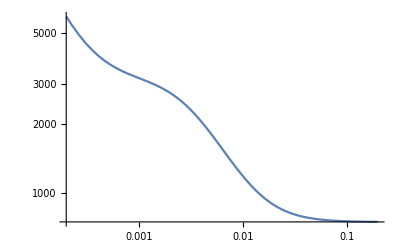

```mathematica
(* convert s domain coefficients to z domain coefficients using bilinear transform *)
sToZ[a0s_, a1s_, a2s_, b0s_, b1s_, b2s_]:={a0s+a1s+a2s,-2 a0s+2 a2s,a0s-a1s+a2s,b0s+b1s+b2s,-2 b0s+2 b2s,b0s-b1s+b2s}

biquadTransferFunctionZ[coefs_,z_]:=(coefs[[4]]+coefs[[5]]/z+coefs[[6]]/z^2)/(coefs[[1]]+coefs[[2]]/z+coefs[[3]]/z^2)

T1 = 3180; T2 = 318; T3 =75;
a0s = T2;
a1s = 1;
a2s=0;
b0s = T1 T3;
b1s = T1+T3;
b2s = 1;

preEmphasisTransferFunctionS[s_]:=(b0s s^2 + b1s s + b2s )/(a0s s^2 + a1s s + a2s)
LogLogPlot[Abs[preEmphasisTransferFunctionS[ⅈ ω]],{ω,0.0002,0.20000}]
```